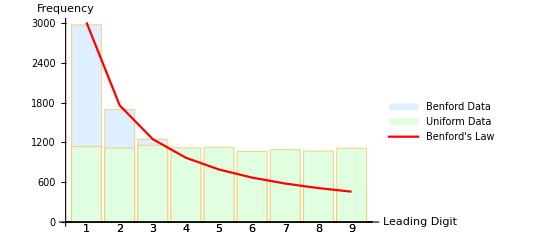

```mathematica
(*Generate Benford's Distribution*)nSamples=10000;
uniformRandoms=RandomReal[{0,1},nSamples];
benfordRandoms=Floor[10^uniformRandoms];
dataBenford=benfordRandoms;

(*Generate uniform distribution 1-9*)
dataUniform=RandomInteger[{1,9},nSamples];

(*Count the occurrences of each digit*)
digitFrequencyBenford=Counts[dataBenford];
digitFrequencyUniform=Counts[dataUniform];

(*Calculate the expected frequency according to Benford's Law*)
benfordLaw=Log[10,1+1/#]&/@Range[9];

(*Visualize the actual distribution and the expected distribution*)
digitFrequencyListBenford=Lookup[digitFrequencyBenford,Range[9],0];
digitFrequencyListUniform=Lookup[digitFrequencyUniform,Range[9],0];
benfordLawList=benfordLaw*nSamples;

barBenford=BarChart[digitFrequencyListBenford,ChartStyle->LightBlue,ChartLegends->{"Benford Data"},ChartLabels->{Range[9]}];
barUniform=BarChart[digitFrequencyListUniform,ChartStyle->LightGreen,ChartLegends->{"Uniform Data"},ChartLabels->{Range[9]}];
line=ListLinePlot[benfordLawList,PlotStyle->Red,PlotLegends->{"Benford's Law"}];

Show[barBenford,barUniform,line,PlotRange->All,AxesLabel->{"Leading Digit","Frequency"}]
```